# Polynomial interpolation

```mathematica
Clear["Global`*"]
```

```mathematica
points={{-3,18},{-1,6},{2,3}};
```

```mathematica
f=Interpolation[points,InterpolationOrder->Length[points]-1];
```

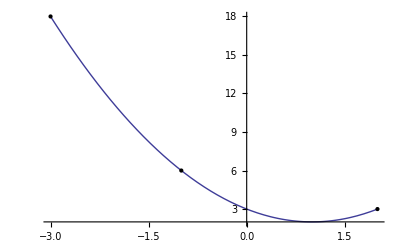

```mathematica
Plot[f[x],{x,Min[points[[All,1]]],Max[points[[All,1]]]}, Epilog->Map[Point, points]]
```

```mathematica
Fit[points, Table[x^n,{n,0,Length[points]-1}], x]
```

3.-2. x+1. x^2

```mathematica
InterpolatingPolynomial[points,x]
```

18+(-5+x) (3+x)

```mathematica
Expand[%]
```

3-2 x+x^2